## Tsetlin Automatons

A two-state Tsetlin Automaton is represented by a positive integer (representing the current state):

```mathematica
3
```

3

Approach is a helper function that takes three inputs, (x, y, t) and outputs x shiftedt closer to y (unless x==y, in which case x is outputted).

```mathematica
Approach[x_?NumberQ,y_?NumberQ,t_?NumberQ]:=
Which[
x==y,x,
x>y,x-t,
x<y,x+t]
```

```mathematica
Approach[3,6,1]
```

4

Most Tsetlin Automaton-related functions take at least the following two arguments as input: the state as well as the state identifier ( a number n such that the total number of states = 2n).

TsetlinAction is a function that takes a current state as well as a state identifier, and outputs a 1 or a 2 (useful for indexing) depending on how the current state compares to the state identifier.

```mathematica
TsetlinAction[t_Integer,si_Integer]:=
If[
t>si,
2,
1]
```

TsetlinPunish and TsetlinReward both take a state and a state identifier as input and punish/reward the Tsetlin automaton. The output is the new state of the Tsetlin Automaton.

```mathematica
TsetlinPunish[t_Integer,si_Integer]:=
If[
t>si,
Approach[t,1,1],
Approach[t,2*si,1]]
```

```mathematica
TsetlinReward[t_Integer,si_Integer]:=
If[
t>si,
Approach[t,2*si,1],
Approach[t,1,1]]
```

```mathematica
TsetlinPunish[4,3]
```

3

```mathematica
TsetlinReward[4,3]
```

5

TsetlinUpdate takes a state, a state identifier, and a number n such that n∈{1,2} and updates the Tsetlin Automaton by rewarding it if it produced output equal to n, or punishing it if it did not. It then outputs the Tsetlin Automaton.

```mathematica
TsetlinUpdate[t_Integer,si_Integer,n_Integer]:=
If[
TsetlinAction[t,si]==n,
TsetlinReward[t,si],
TsetlinPunish[t,si]]
```

Train a Tsetlin Automaton 10 times on a definite two-armed bandit problem.

```mathematica
definite2ArmBanditLearnList=NestList[ (* should learn 1, which always wins here *)
TsetlinUpdate[
#,
3,
Position[
#,
TakeLargestBy[#,#&,1]⟦1⟧]⟦1⟧⟦1⟧&@{1,0}]&,
3,10]
```

{3,2,1,1,1,1,1,1,1,1,1}

```mathematica
TsetlinAction[definite2ArmBanditLearnList[[-1]],3] (* outputs the final action choice of the automaton *)
```

1

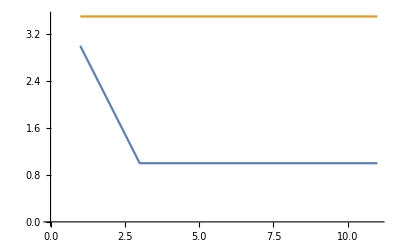

```mathematica
ListLinePlot[{definite2ArmBanditLearnList,Table[3.5,{x,definite2ArmBanditLearnList}] }] (* plot the learning curve of the automaton *)
```

Train a Tsetlin Automaton 10 times on an indefinite two-armed bandit problem.

```mathematica
indefinite2ArmBanditLearnList=NestList[ (* should learn 1, which usually (not always) wins here *)
TsetlinUpdate[
#,
3,
Position[
#,
TakeLargestBy[#,#&,1]⟦1⟧]⟦1⟧⟦1⟧&@{RandomVariate[NormalDistribution[0.75,.5]],RandomVariate[NormalDistribution[0.25,.5]]}]&,
4,10]
```

{4,3,2,1,1,1,1,1,1,1,1}

```mathematica
TsetlinAction[indefinite2ArmBanditLearnList[[-1]],3] (* outputs the final action choice of the automaton *)
```

1

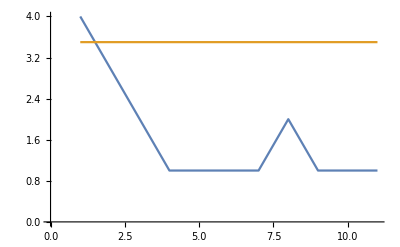

```mathematica
ListLinePlot[{indefinite2ArmBanditLearnList,Table[3.5,{x,indefinite2ArmBanditLearnList}] }](* plot the learning curve of the automaton *)
```

TsetlinWeightedReward rewards the Tsetlin Automaton if a random number from 0 to 1 is greater than the third argument, which is a number. In practical use, the third number is usually generated by applying a function.

```mathematica
TsetlinWeightedReward[t_Integer,si_Integer,pf_?NumericQ]:=
If[
RandomReal[]≤pf,
TsetlinReward[t,si],
t]
```

```mathematica
TsetlinWeightedReward[3,3,1]
```

3

```mathematica
TsetlinWeightedReward[3,3,1000]
```

2

TsetlinWeightedPunish is the punish equivalent of TsetlinWeightedReward.

```mathematica
TsetlinWeightedPunish[t_Integer,si_Integer,pf_?NumericQ]:=
If[
RandomReal[]≤pf,
TsetlinPunish[t,si],
t]
```

## Tsetlin Machine Basic Structure

Before the complete Tsetlin Machine head architecture is established, some heads important for building them need to be shown.

TsetlinClause[l, lneg] is a head that takes two arguments: the Tsetlin Automatons corresponding to the inputs as well as the ones corresponding to the negated inputs. TsetlinClauseNonNegated, when applied to a TsetlinClause, returns the list of automatons corresponding to the non-negated inputs. TsetlinClauseNegated returns the list of automatons corresponding to the negated inputs.

```mathematica
TsetlinClauseNonNegated[tc_TsetlinClause]:=tc[[1]]
```

```mathematica
TsetlinClauseNegated[tc_TsetlinClause]:=tc[[2]]
```

TsetlinOutput[l, f] is a head that takes two arguments: a list of conjunctive clauses and a function. It, when in use in a complete Tsetlin machine, reduces the outputs of each of the conjunctive clauses by applying the function, and returns the final output. TsetlinOutputClauses outputs the list of TsetlinClauses of a TsetlinOutput, and TsetlinOutputFunction returns the function.

```mathematica
TsetlinOutputClauses[to_TsetlinOutput]:=to[[1]]
```

```mathematica
TsetlinOutputFunction[to_TsetlinOutput]:=to[[2]]
```

TsetlinMachine[lc, si] is a head that represents a single-layer Tsetlin Machine. It takes two arguments: a list of TsetlinOutputs and the state identifier it uses for all of it’s automatons. Here is an example of a Tsetlin Machine that takes three inputs and produces two outputs (where each output has two clauses):

```mathematica
tm0=TsetlinMachine[
{
TsetlinOutput[
{
TsetlinClause[
{3,4,3},{4,4,3}],
TsetlinClause[
{3,3,3},{4,4,4}]
},
Or],
TsetlinOutput[
{
TsetlinClause[
{6,5,2},{3,2,4}],
TsetlinClause[
{2,3,2},{1,2,5}]
},
Or]
},
3]
```

TsetlinMachine[{TsetlinOutput[{TsetlinClause[{3,4,3},{4,4,3}],TsetlinClause[{3,3,3},{4,4,4}]},Or],TsetlinOutput[{TsetlinClause[{6,5,2},{3,2,4}],TsetlinClause[{2,3,2},{1,2,5}]},Or]},3]

TsetlinMachineOutputs takes a TsetlinMachine as input, and outputs the list of outputs,

```mathematica
TsetlinMachineOutputs[tm_TsetlinMachine]:=tm[[1]]
```

```mathematica
TsetlinMachineOutputs[tm0]
```

{TsetlinOutput[{TsetlinClause[{3,4,3},{4,4,3}],TsetlinClause[{3,3,3},{4,4,4}]},Or],TsetlinOutput[{TsetlinClause[{6,5,2},{3,2,4}],TsetlinClause[{2,3,2},{1,2,5}]},Or]}

TsetlinMachineStateIdentifier takes a TsetlinMachine as input, and outputs the StateIdentifier of the machine.

```mathematica
TsetlinMachineStateIdentifier[tm_TsetlinMachine]:=tm[[2]]
```

```mathematica
TsetlinMachineStateIdentifier[tm0]
```

3

Inputs in a Tsetlin machine are given in binary. Numerical input can be given, but the numbers need to be converted to binary (a list of boolean values). As such, a maximum and minimum value need to be established. Hopefully I can develop a system so that the programmer does not need to worry about this (e.g. handled automatically) but for now this has to be done manually.
An example list of inputs to a Tsetlin machine: {False,False,False,False,True,True,False,True} (representing integer 13).

For the Tsetlin Automatons in the machine, 1 represents “exclude input” and 2 represents “include input”

TsetlinClauseSelectedInputs  takes a TsetlinClause, state identifier, and list of inputs. It returns a list of the inputs that the Tsetlin automaton of the clause have selected.

```mathematica
TsetlinClauseSelectedInputs[tc_TsetlinClause,si_Integer,li_List]:=
Last/@
Select[
Join[
Transpose[{
(TsetlinAction[#,si]&/@TsetlinClauseNonNegated[tc]),
li}],
Transpose[{
(TsetlinAction[#,si]&/@TsetlinClauseNegated[tc]),
Not/@li}]],
#[[1]]==2&]
```

```mathematica
TsetlinClauseSelectedInputs[ (* should output {True, True, False} *)
TsetlinClause[
{1,3,5},
{2,4,6}],
3,
{True, False, True}]
```

{True,True,False}

TsetlinClauseOutput takes a TsetlinClause, state identifier, and list of inputs as it’s arguments. It outputs either a 1 or 0, depending on the result of ANDing the selected inputs of the clause.

```mathematica
TsetlinClauseOutput[tc_TsetlinClause,si_Integer,li_List]:=
Fold[
And,
True,
TsetlinClauseSelectedInputs[tc,si,li]]
```

```mathematica
TsetlinClauseOutput[ (* should output False *)
TsetlinClause[
{1,3,5},
{2,4,6}],
3,
{True, False, True}]
```

False

TsetlinOutputResult takes a TsetlinOutput, state identifier, and list of inputs as it’s arguments. It returns the result of fold-applying the function of the TsetlinOutput to the TsetlinClause outputs calculated with the given state identifier and input.

```mathematica
TsetlinOutputResult[to_TsetlinOutput,si_Integer,li_List]:=
Fold[
TsetlinOutputFunction[to],
Map[
TsetlinClauseOutput[#,si,li]&,
TsetlinOutputClauses[to]]]
```

```mathematica
TsetlinOutputResult[ (* should output True *)
TsetlinOutput[
{TsetlinClause[
{1,3,5},
{2,4,6}],
TsetlinClause[
{6,1,6},
{1,1,2}]},
Or],
3,
{True, False, True}]
```

True

TsetlinMachineCalculateOutputs takes a TsetlinMachine and a list of inputs as input, and outputs a list of the outputs. This is the way to apply trained Tsetlin machines.

```mathematica
TsetlinMachineCalculateOutputs[tm_TsetlinMachine,li_List]:=
Map[
TsetlinOutputResult[
#,
TsetlinMachineStateIdentifier[tm],
li]&,
TsetlinMachineOutputs[tm]]
```

```mathematica
TsetlinMachineCalculateOutputs[ (* Should return {True, False} *)
TsetlinMachine[
{
TsetlinOutput[
{TsetlinClause[
{1,3,5},
{2,4,6}],
TsetlinClause[
{6,1,6},
{1,1,2}]},
Or],
TsetlinOutput[
{TsetlinClause[
{1,5,1},
{2,1,1}],
TsetlinClause[
{1,1,2},
{5,1,2}]},
Or]},
3],
{True, False, True}]
```

{True,False}

## Initializing a Tsetlin Machine

First, some functions for building the structure of Tsetlin machines (introduced from bottom up).

InitializeTsetlinAutomatonList takes 2 arguments: the state identifier and the length of the input.

```mathematica
InitializeTsetlinAutomatonList[si_Integer,il_Integer]:=
Table[RandomInteger[]+si,il]
```

```mathematica
InitializeTsetlinAutomatonList[3,3]
```

{3,3,4}

InitializeTsetlinClause takes 2 arguments: the state identifier and the length of the input.

```mathematica
InitializeTsetlinClause[si_Integer,il_Integer]:=
TsetlinClause[InitializeTsetlinAutomatonList[si,il],InitializeTsetlinAutomatonList[si,il]]
```

```mathematica
InitializeTsetlinClause[3,3]
```

TsetlinClause[{4,3,4},{4,3,4}]

InitializeTsetlinOutput takes 4 arguments: the state identifier, the length of the input, the number of clauses per the output, and the output function.

```mathematica
InitializeTsetlinOutput[si_Integer,il_Integer,nc_Integer, f_]:=
TsetlinOutput[
Table[
InitializeTsetlinClause[si,il],
nc],
f]
```

```mathematica
InitializeTsetlinOutput[3,3,2,Or]
```

TsetlinOutput[{TsetlinClause[{3,3,4},{4,3,4}],TsetlinClause[{4,4,4},{4,3,3}]},Or]

InitializeTsetlinMachine takes 4 arguments: the state identifier, the length of the input, the number of clauses per each output, and a list consisting of the output functions (the length of the list implicitly is equal to the number of outputs).

```mathematica
InitializeTsetlinMachine[si_Integer,il_Integer,nc_Integer,lf_List]:=
TsetlinMachine[
Map[
InitializeTsetlinOutput[
si,
il,
nc,
#]&,
lf],
si]
```

```mathematica
InitializeTsetlinMachine[3,3,2,{Or}]
(* Should produce something like:
TsetlinMachine[
{TsetlinOutput[
{
TsetlinClause[
{3,4,3},
{4,4,3}],
TsetlinClause[
{4,3,4},
{4,3,3}]},
Or]},
3] *)
```

```mathematica
TsetlinMachine[{TsetlinOutput[{TsetlinClause[{3,4,3},{3,3,4}],TsetlinClause[{4,4,3},{3,4,4}]},Or]},3].
```

## Training a Tsetlin Machine

TsetlinType1Feedback takes 5 arguments: an integer representing a Tsetlin Automaton, the state identifier, the input value the Tsetlin Automaton corresponds to, and the target output of the clause, and an “s” value which controls how fine-grained the patterns learned are.. It outputs the Tsetlin Automaton but rewarded or punished using type 1 feedback.

```mathematica
TsetlinType1Feedback[ta_Integer,si_Integer,i_Boolean,to_Boolean,s_?NumericQ]:=
If[
(ta>si),
If[  (* automata that include input *)
to,
If[ (* target value == True *)
i,
TsetlinWeightedReward[ta,si,((s-1)/s)],
ta],
TsetlinWeightedPunish[ta,si,(1/s)](* target value == False *)],
If[ (* automata that exclude input *)
to,
If[ (* target value == True *)
i,
TsetlinWeightedPunish[ta,si,((s-1)/s)],
TsetlinWeightedReward[ta,si,(1/s)]],
TsetlinWeightedReward[ta,si,(1/s)] (* target value == False *)]]
```

```mathematica
TsetlinType1Feedback[3,3,True,True,1]
```

3

TsetlinType2Feedback takes 4 arguments: an integer representing a Tsetlin Automaton, the state identifier, the input value the Tsetlin Automaton corresponds to, and the target output of the clause.

```mathematica
TsetlinType2Feedback[ta_Integer,si_Integer,i_Boolean,to_Boolean]:=
If[
((ta<si)&&to&&!i),
TsetlinPunish[ta,si],
ta]
```

```mathematica
TsetlinType2Feedback[3,3,True,False]
```

4

TsetlinType1ClauseFeedback takes 4 arguments: a TsetlinClause, a state identifier, the list of inputs, the target output of the clause, and an s value. It returns a TsetlinClause where TsetlinType1Feedback has been applied to each Tsetlin Automaton.

```mathematica
TsetlinType1ClauseFeedback[tc_TsetlinClause,si_Integer,i_List,to_Boolean,s_?NumericQ]:=
TsetlinClause[
MapThread[
TsetlinType1Feedback[#1,si,#2,to,s]&,
{TsetlinClauseNonNegated[tc],
i}],
MapThread[
TsetlinType1Feedback[#1,si,#2,to,s]&,
{TsetlinClauseNegated[tc],
Not/@i}]]
```

```mathematica
Nest[
TsetlinType1ClauseFeedback[
#,
3,
{True,False,True},
True,
9]&,
TsetlinClause[
{3,2,3},
{4,3,1}],
30]
```

TsetlinClause[{6,1,6},{4,6,1}]

TsetlinType2ClauseFeedback takes 4 inputs: the TsetlinClause, the state identifier, the list of inputs, and the target output value. It returns a TsetlinClause where TsetlinType2Feedback has been applied to each Tsetlin Automaton.

```mathematica
TsetlinType2ClauseFeedback[tc_TsetlinClause,si_Integer,i_List,to_Boolean]:=
TsetlinClause[
MapThread[
TsetlinType2Feedback[#1,si,#2,to]&,
{TsetlinClauseNonNegated[tc],
i}],
MapThread[
TsetlinType2Feedback[#1,si,#2,to]&,
{TsetlinClauseNegated[tc],
Not/@i}]]
```

```mathematica
Nest[
TsetlinType2ClauseFeedback[
#,
3,
{True,False,True},
True]&,
TsetlinClause[
{1,3,5},
{2,4,6}],
2]
```

TsetlinClause[{1,3,5},{3,4,6}]

TsetlinOutputFeedback takes 6 arguments: a TsetlinOutput, the state identifier, a list of the input, the desired output,  s (precision) and a function. The function should take a TsetlinClause and it’s position in the OutputClause as input, and output a the number corresponding to the type of feedback (either 1 or 2, corresponding to type 1 or 2 feedback.

```mathematica
TsetlinOutputFeedback[to_TsetlinOutput,si_Integer, i_List,do_,s_?NumericQ, whichFeedback_]:=
TsetlinOutput[
MapThread[
{
TsetlinType1ClauseFeedback[#1,si,#2,do,s],
TsetlinType2ClauseFeedback[#1,si,#2,do]}⟦whichFeedback[#1,#3]⟧&,
{
TsetlinOutputClauses[to],
Table[i,Length[TsetlinOutputClauses[to]]],
Range[Length[TsetlinOutputClauses[to]]]}],
TsetlinOutputFunction[to]]
```

```mathematica
TsetlinOutputFeedback[
TsetlinMachineOutputs[InitializeTsetlinMachine[
3,
3,
2,
{Or}]]⟦1⟧,
3,
{True,False,True},
True,
3,
1&]
```

TsetlinOutput[{TsetlinClause[{5,4,4},{2,4,4}],TsetlinClause[{5,4,4},{4,4,4}]},Or]

TsetlinMachineUpdate takes 5 arguments: a TsetlinMachine, a list of inputs, the list of expected outputs, and an s-value (precision), and a function (same purpose as in TsetlinOutputFeedback). It returns the TsetlinMachine where each output has been trained on the input with the desired output.

```mathematica
TsetlinMachineUpdate[tm_TsetlinMachine,input_List,output_List,s_?NumericQ,whichFeedback_]:=
TsetlinMachine[
MapThread[
TsetlinOutputFeedback[
#1,
TsetlinMachineStateIdentifier[tm],
input,
#2,
s,
whichFeedback]&,
{
TsetlinMachineOutputs[tm],
output}],
TsetlinMachineStateIdentifier[tm]]
```

```mathematica
TsetlinMachineUpdate[
InitializeTsetlinMachine[
3,
3,
2,
{Or}],
{True,False,True},{True},
3,
1&]
```

TsetlinMachine[{TsetlinOutput[{TsetlinClause[{4,3,3},{4,4,2}],TsetlinClause[{4,2,5},{3,5,4}]},Or]},3]

TsetlinMachineCompleteUpdate takes a TsetlinMachine, a list of rules or a rule from inputs to expected outputs, an s-value (precision), and a function that selects between Type 1 and Type 2 feedback (as explained before). It outputs a TsetlinMachine that has been trained once on every input to every output.

```mathematica
TsetlinMachineCompleteUpdate[tm_TsetlinMachine,trainDataInput:(_List|_Rule),s_?NumericQ,whichFeedback_]:=
Module[
{trainData=
RandomSample@
If[ListQ@trainDataInput,
trainDataInput,
Rule@@@Partition[#, 2]&@Riffle[#[[1]], #[[2]]]&@trainDataInput]},
Fold[
TsetlinMachineUpdate[
#1,
Keys[Association@#2][[1]],
Values[Association@#2][[1]],
s,
whichFeedback]&,
tm,
trainData]]
```

```mathematica
TsetlinMachineCompleteUpdate[
InitializeTsetlinMachine[
3,
2,
2,
{Or}],
{{False,False},{False,True},{True,False},{True,True}}-> {{False},{True},{True},{False}},
3,
1&]
```

TsetlinMachine[{TsetlinOutput[{TsetlinClause[{3,4},{3,3}],TsetlinClause[{5,3},{4,5}]},Or]},3]

TsetlinMachineTest takes 2 arguments: a TsetlinMachine and test data. It returns the percentage of correct outputs.

```mathematica
TsetlinMachineTest[tm_TsetlinMachine,testDataInput:(_List|_Rule)]:=
Module[
{testData=
If[ListQ@testDataInput,
testDataInput,
AssociationThread@testDataInput]},
Echo[Total[
MapThread[
Equal,
{((TsetlinMachineCalculateOutputs[tm,#])&/@
Keys@Association@testData),
Values@Association@testData}]/.{True->1,False->0}]/Length@testData]]
```

```mathematica
TsetlinMachineTest[
InitializeTsetlinMachine[
3,
2,
2,
{Or}],
{{False,False},{False,True}}->{{False},{True}}]
```

0

0

TsetlinMachineHiddenTest is the same as TsetlinMachineTest, except that it outputs the TsetlinMachine it was given as an argument.

```mathematica
TsetlinMachineHiddenTest[tm_TsetlinMachine,testDataInput:(_List|_Rule)]:=
(TsetlinMachineTest[tm,testDataInput];
tm)
```

```mathematica
TsetlinMachineHiddenTest[
InitializeTsetlinMachine[
3,
2,
2,
{Or}],
{{False,False},{False,True}}->{{False},{True}}]
```

1

TsetlinMachine[{TsetlinOutput[{TsetlinClause[{4,4},{4,4}],TsetlinClause[{4,4},{4,4}]},Or]},3]

TsetlinMachineTrain takes 6 arguments: a TsetlinMachine, training data in rule form, test data in rule form, a stop criteria, and a function that decides which feedback to give. The stop criteria can be either a real number less than or equal to 1, or an Integer. A real number represents the desired accuracy of the TsetlinMachine, and an Integer represents the number of times the machine should be trained.

```mathematica
TsetlinMachineTrain[tm_TsetlinMachine,trainDataInput:(_List|_Rule),testDataInput:(_List|_Rule),stopCriteria_?NumericQ,s_?NumericQ,whichFeedback_]:=
If[
IntegerQ@stopCriteria,
Nest[
TsetlinMachineHiddenTest[
TsetlinMachineCompleteUpdate[
#1,
trainDataInput,
s,
whichFeedback],
testDataInput]&,
tm,
stopCriteria],
NestWhile[
TsetlinMachineCompleteUpdate[
Echo@#,
trainDataInput,
s,
whichFeedback]&,
tm,
(TsetlinMachineTest[#,testDataInput]<stopCriteria)&]]
```

Train a TsetlinMachine on XOR until it has 100% accuracy:

```mathematica
xormachine=TsetlinMachineTrain[
InitializeTsetlinMachine[
3,
2,
4,
{Or}],
{{False,False},{False,True},{True,False},{True,True}}->{{False},{True},{True},{False}},
{{False,False},{False,True},{True,False},{True,True}}->{{False},{True},{True},{False}},
1.,
3,
RandomInteger[{1,2}]&]
```

1/2

TsetlinMachine[{TsetlinOutput[{TsetlinClause[{3,4},{4,3}],TsetlinClause[{3,3},{3,3}],TsetlinClause[{3,3},{3,4}],TsetlinClause[{3,3},{4,4}]},Or]},3]

1/2

TsetlinMachine[{TsetlinOutput[{TsetlinClause[{2,4},{4,3}],TsetlinClause[{3,3},{4,3}],TsetlinClause[{2,1},{4,5}],TsetlinClause[{2,2},{4,3}]},Or]},3]

1/2

TsetlinMachine[{TsetlinOutput[{TsetlinClause[{3,4},{4,4}],TsetlinClause[{3,3},{3,3}],TsetlinClause[{3,1},{3,6}],TsetlinClause[{3,3},{4,3}]},Or]},3]

3/4

TsetlinMachine[{TsetlinOutput[{TsetlinClause[{2,5},{5,4}],TsetlinClause[{3,3},{3,4}],TsetlinClause[{4,1},{3,6}],TsetlinClause[{3,3},{4,3}]},Or]},3]

1/2

TsetlinMachine[{TsetlinOutput[{TsetlinClause[{1,5},{6,4}],TsetlinClause[{3,3},{4,3}],TsetlinClause[{5,1},{3,5}],TsetlinClause[{3,2},{3,3}]},Or]},3]

1/2

TsetlinMachine[{TsetlinOutput[{TsetlinClause[{1,6},{6,4}],TsetlinClause[{4,4},{4,4}],TsetlinClause[{5,2},{3,5}],TsetlinClause[{3,2},{3,4}]},Or]},3]

1/2

TsetlinMachine[{TsetlinOutput[{TsetlinClause[{3,6},{6,3}],TsetlinClause[{4,3},{5,5}],TsetlinClause[{5,2},{3,5}],TsetlinClause[{3,3},{3,3}]},Or]},3]

1/2

TsetlinMachine[{TsetlinOutput[{TsetlinClause[{3,6},{5,2}],TsetlinClause[{4,3},{5,5}],TsetlinClause[{4,4},{3,4}],TsetlinClause[{2,3},{3,3}]},Or]},3]

3/4

TsetlinMachine[{TsetlinOutput[{TsetlinClause[{1,5},{5,2}],TsetlinClause[{5,1},{6,6}],TsetlinClause[{5,4},{3,5}],TsetlinClause[{3,3},{3,4}]},Or]},3]

1

TsetlinMachine[{TsetlinOutput[{TsetlinClause[{2,4},{5,3}],TsetlinClause[{4,1},{5,6}],TsetlinClause[{5,3},{3,5}],TsetlinClause[{4,2},{3,4}]},Or]},3]